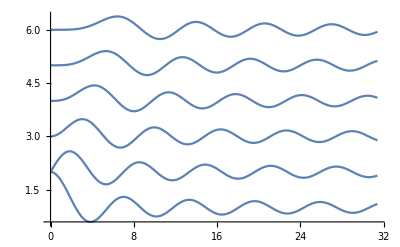

```mathematica
Plot[Table[BesselJ[n,x]+(n+1),{n,0, 5}],{x, 0, 10 π}, PlotRange->All]
```

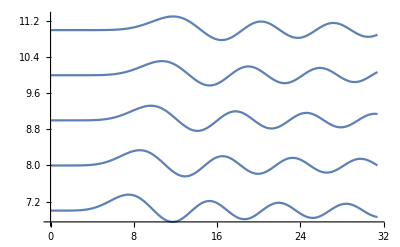

```mathematica
Plot[Table[BesselJ[n,x]+(n+1),{n,6,10}],{x, 0, 10 π}, PlotRange->All]
```

```mathematica
D[BesselJ[n,x],x]
```

```mathematica
Integrate[BesselJ[n,x],x]
```

```mathematica
Plot[Table[AiryAi[ x/k],{k, -5, 5,2}],{x,-10,10},PlotStyle->{Darker@Magenta,DropShadowing[]}, Axes->False]
```

-Graphics-

```mathematica
Plot[Table[(n+1)+2^(-1-n) x^(1+n) Gamma[(1+n)/2] HypergeometricPFQRegularized[{(1+n)/2},{1+n,(3+n)/2},-x^2/4], {n,0, 4}], {x, 0, 10 π}, Axes->False, PlotStyle->{Darker@Blue, DropShadowing[]}]
```

-Graphics-

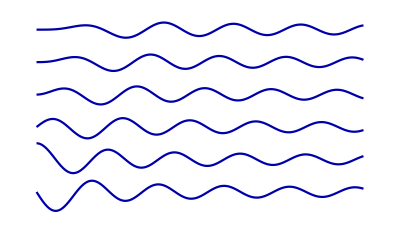

```mathematica
Plot[Table[1/2 (BesselJ[-1+n,x]-BesselJ[1+n,x])+(n+1), {n,0,5}], {x, 0, 10 π}, Axes->False, PlotStyle->Darker@Blue]
```